```mathematica
ClearAll["Global`*"]
α=-52.4048
β=-0.4628
γ=-185.1555
k=27.3976
ϕ0=-529.7076
Mp = 1
M = Mp * Sqrt[2]

μ = 10
λ= 0
κ = 0
q = 0
li = 0
```

-52.4048

-0.4628

-185.156

27.3976

-529.708

1

√2

10

0

0

0

«1 more identical outputs»

```mathematica
A[φ_]:=(β*φ^2+γ*ϕ0*φ+α*ϕ0^2)
K[φ_]:=M^2 (-(36*β)/(β*φ^2+γ*ϕ0*φ+α*ϕ0^2)+(ϕ0^2*(γ^2-4*β*α)*(k-6))/(2(β*φ^2+γ*ϕ0*φ+α*ϕ0^2)^2))
V[φ_]:= M^4/(2(β*φ^2+γ*ϕ0*φ+α*ϕ0^2)^2)*(κ*ϕ0^4+li*φ*ϕ0^3+μ^2*ϕ0^2*φ^2+q*ϕ0*φ^3+λ*φ^4)
A[φ]
K[φ]
V[φ]
```

-1.47043×10^7+98078.3 φ-0.4628 φ^2

2 ((1.02624×10^11)/((-1.47043×10^7+98078.3 φ-0.4628 φ^2)^2)+16.6608/(-1.47043×10^7+98078.3 φ-0.4628 φ^2))

(2 (0.+2.8059×10^7 φ^2))/((-1.47043×10^7+98078.3 φ-0.4628 φ^2)^2)

```mathematica
α=-1.9272
β=-4.7452
γ=0.0893
k=0.1244
ϕ0=0.1304
μ=0.1079

λ=-0.0004
κ=0.1056
χ=-1.2946
ω=0.1169
```

-1.9272

-4.7452

0.0893

0.1244

0.1304

0.1079

-0.0004

0.1056

-1.2946

0.1169

```mathematica
A[x_]:= β*ϕ0^2+γ*ϕ0*x+α*x^2
A[x]
```

-0.0806881+0.0116447 x-1.9272 x^2

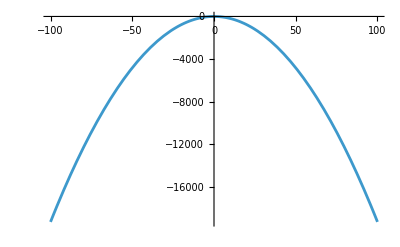

```mathematica
Plot[A[x],{x,-100,100}]
```

```mathematica
Solve[A[x]==0,x]
```

{{x→0.00302115-0.204595 ⅈ},{x→0.00302115+0.204595 ⅈ}}

```mathematica
V[x_]:= (κ*ϕ0^4+ 2*ω*ϕ0^3*x + μ*ϕ0^2*x^2 + χ*ϕ0*x^3 + λ*x^4)/A[x]
V[x]
```

(0.0000305333+0.000518415 x+0.00183475 x^2-0.168816 x^3-0.0004 x^4)/(-0.0806881+0.0116447 x-1.9272 x^2)

```mathematica
Plot[V[x],{x,-100,100}]
V[0]
```

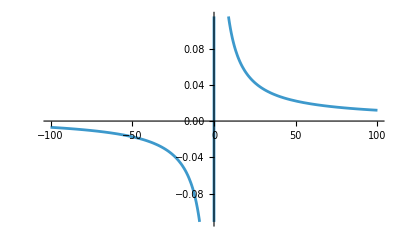

```mathematica
f[x_]:=V'[x]/V[x]
Plot[f[x],{x,-100,100}]
```

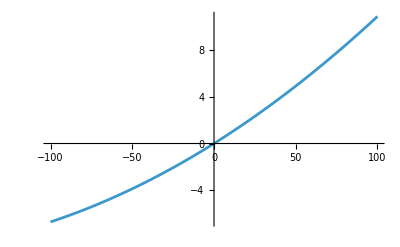

```mathematica
f[x_]:=Log[V[x]]
f'[x]
Plot[f'[x],{x,-100,100}]
```

((-0.0806881+0.0116447 x-1.9272 x^2) ((0.000518415+0.0036695 x-0.506448 x^2-0.0016 x^3)/(-0.0806881+0.0116447 x-1.9272 x^2)-((0.0116447-3.8544 x) (0.0000305333+0.000518415 x+0.00183475 x^2-0.168816 x^3-0.0004 x^4))/((-0.0806881+0.0116447 x-1.9272 x^2)^2)))/(0.0000305333+0.000518415 x+0.00183475 x^2-0.168816 x^3-0.0004 x^4)

-Graphics-